For input parameters m and n, the number of vertices generated is n*m.

```mathematica
nearestHexPoints[point_,coordinates_] := Map[point <-> # &, Nearest[coordinates, point, {7, 2}]][[2;;]]
hexagonalGraphGen[n_, m_] :=Module[{coordinates,edges},
coordinates=Flatten[Table[{i*Sqrt[3],j},{i,1,n},{j,Mod[i, 2],(m-1)*2, 2}], 1];
edges=DeleteDuplicates[Sort /@ Flatten[Map[nearestHexPoints[#,coordinates]&, coordinates], 1]];
Graph[coordinates, edges, VertexCoordinates -> coordinates]
]
```

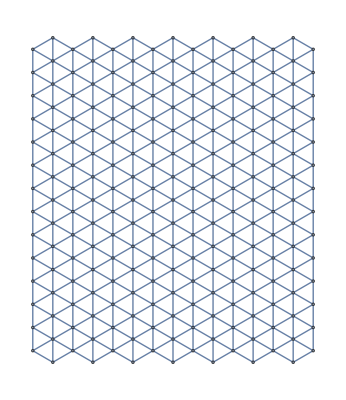

```mathematica
hexagonalGraphGen[15,15]
```

```mathematica
neighbors[graph_Graph, vertex_List] := VertexOutComponent[graph, vertex, 1]
```

```mathematica
neighbors[graph,{Sqrt[3],1}]
```

{{√3,1},{√3,3},{2 √3,0},{2 √3,2}}

```mathematica
labelVerticesByNumber[graph_Graph]:=Fold[Annotate[{#1,#2[[1]]},VertexLabels->ToString[#2[[2]]]]&,graph,Transpose[{VertexList[graph],Range[Length[VertexList[graph]]]}]]
```

```mathematica
groundHeightTestFunction[vertexCoordinate_List]:=vertexCoordinate[[1]]/5
waterHeightTestFunction[vertexCoordinate_List]:=1
```

```mathematica
(*node density is the number of nodes per square km inside the geo range, meaning the number of nodes n, can be expressed with the equation n = nodeDensity * geoRange^2*)
initializeCellularAutomata[geoPosition_GeoPosition,geoRange_,nodeDensity_,waterLevelFunction_]:=Module[{graphLength,coefficient,geoCoordinatesOfEachNode,heights},
graphLength=Sqrt[nodeDensity]*geoRange;
graph=hexagonalGraphGen[graphLength,graphLength];
coefficient=geoRange/VertexList[graph][[-1]][[1]];
geoCoordinatesOfEachNode=(geoPosition[[1]]-{geoRange,geoRange}/2+#*coefficient)&/@VertexList[graph] ;
heights=QuantityMagnitude@GeoElevationData[GeoPosition[geoCoordinatesOfEachNode]];

vertexData=AssociationThread[VertexList[graph],MapIndexed[<|"groundHeight"->heights[[#2]][[1]],
	"waterLevel"->If[NumberQ[waterLevelFunction],waterLevelFunction,waterLevelFunction[#1]],
	"drainAmount"->{}|>&,VertexList[graph]]]
]
```

```mathematica
vertexData=Nothing;
initVertexData[groundHeightFunction_,waterLevelFunction_]:=(graph=hexagonalGraphGen[15,15];vertexData=AssociationThread[VertexList[graph],<|"groundHeight"->groundHeightFunction[#],
	"waterLevel"->waterLevelFunction[#],
	"drainAmount"->{}|>&/@VertexList[graph]])
If[vertexData==Nothing,initVertexData[groundHeightTestFunction,waterHeightTestFunction]];
```

```mathematica
visualizeGraph[graph_Graph,vertexData_]:=SimpleGraph[graph,VertexSize->((#->vertexData[#]["groundHeight"]+vertexData[#]["waterLevel"])&)/@VertexList[graph]]
visualizeGraph[graph_Graph,vertexData_,waterLevelSizeWeight_,groundLevelSizeWeight_]:=SimpleGraph[graph,VertexSize->((#->(vertexData[#]["groundHeight"]*groundLevelSizeWeight+vertexData[#]["waterLevel"]*waterLevelSizeWeight)&)/@VertexList[graph])]
```

```mathematica
visualizeGraph3D[graph_Graph,vertexData_] := ListPointPlot3D[{Join[#, {vertexData[#]["groundHeight"]}] & /@ VertexList[graph], Join[#, {vertexData[#]["groundHeight"] + vertexData[#]["waterLevel"]}] & /@ VertexList[graph]}]
visualizeGraph3D[graph_Graph,vertexData_,waterLevelScale_,groundHeightScale_] := ListPointPlot3D[{Join[#, {vertexData[#]["groundHeight"]*groundHeightScale}] & /@ VertexList[graph], Join[#, {vertexData[#]["groundHeight"]*groundHeightScale + vertexData[#]["waterLevel"]*waterLevelScale}] & /@ VertexList[graph]}]
```

```mathematica
calculateNeighborhoodNewWaterLevels[graph_Graph,vertex_List,flowRate_]:=Module[{neighborhood,W,H,k=0,heights,assoc},
	(*sort neighborhood by ground height*)
	neighborhood=SortBy[neighbors[graph,vertex],(vertexData[#]["groundHeight"])&];
	heights=(vertexData[#]["groundHeight"])&/@neighborhood;

	W=Total[vertexData[#]["waterLevel"]&/@neighborhood]; (*calculate the total "volume" of water*)
	Table[If[Sum[heights[[k1]] - heights[[ihi2]], {ihi2,1, k1}] ≤ W, k = k1; Return["Exit",Table]],{k1,Length[neighborhood],1,-1}]; (*calculate k *)
	H = (W + Sum[heights[[ihi]], {ihi,1, k}])/k;
	AppendTo[vertexData[#]["drainAmount"],vertexData[#]["waterLevel"] + (H - (vertexData[#]["groundHeight"]+vertexData[#]["waterLevel"])) * (1-flowRate)]&/@neighborhood[[;;k]];
	AppendTo[vertexData[#]["drainAmount"],flowRate * vertexData[#]["waterLevel"]]&/@neighborhood[[k+1;;]];
]
```

```mathematica
calculateGraphNewWaterLevels[graph_Graph]:=calculateNeighborhoodNewWaterLevels[graph,#,0.9]&/@VertexList[graph]
```

```mathematica
updateGraphWaterLevels[graph_Graph]:=(vertexData[#]["waterLevel"]=Mean[vertexData[#]["drainAmount"]];vertexData[#]["drainAmount"]={})&/@VertexList[graph]
```

```mathematica
fullUpdateGraph[graph_Graph]:=(calculateGraphNewWaterLevels[graph];updateGraphWaterLevels[graph];vertexData)
```

```mathematica
generateWaterData[iterations_]:=(generatedData={};
Do[AppendTo[generatedData,fullUpdateGraph[graph]],{i,10}];generatedData)
```

```mathematica
initVertexData[groundHeightTestFunction,waterHeightTestFunction];
generatedData=generateWaterData[10];
ListAnimate[visualizeGraph3D[graph,#]&/@generatedData]
```

```mathematica
initializeCellularAutomata[GeoPosition[],10,2,1000]
generatedData=generateWaterData[100];
ListAnimate[visualizeGraph3D[graph,#]&/@generatedData]
```

ListAnimate[Null]